```mathematica
Quit
```

## Setup

```mathematica
AppendTo[$Path,"C:\\Users\\micha\\OneDrive\\Desktop\\Oden\\Notes\\Equivariant-Polynomial-Tensor-Functions-main\\Equivariant-Polynomial-Tensor-Functions-main"];
```

```mathematica
Needs["Instrumentation`"]
```

Instrumentation::versions: CodeParser version 1.13 and Instrumentation version 1.10 are different. There may be unexpected problems. Evaluate PacletInstall /@ {"CodeParser", "Instrumentation"} to get the latest versions.

```mathematica
Quiet[DeleteDirectory[FileNameJoin[{$TemporaryDirectory,"Collatz-example"}],DeleteContents->True],{DeleteDirectory::nodir}];
tmp=CreateDirectory[FileNameJoin[{$TemporaryDirectory,"Collatz-example"}]];
```

```mathematica
file=File["/oden/mliu/HarvestMultiplicitySpaceTree.wl"];
file=File["C:\\Users\\micha\\OneDrive\\Desktop\\Oden\\Notes\\Equivariant-Polynomial-Tensor-Functions-main\\Equivariant-Polynomial-Tensor-Functions-main\\GrowMultiplicitySpaceTree.wl"];
```

```mathematica
CreateDirectory[FileNameJoin[{tmp,"Collatz-orig","Collatz"}],CreateIntermediateDirectories->True];
CopyFile[file,FileNameJoin[{tmp,"Collatz-orig","Collatz","Profile.wl"}]];
```

```mathematica
ProfileInstrument[FileNameJoin[{tmp,"Collatz-orig","Collatz"}],FileNameJoin[{FileNameJoin[{tmp,"Collatz-profile","Collatz"}]}]]
```

```mathematica
PrependTo[$Path,FileNameJoin[{tmp,"Collatz-profile","Collatz"}]];
```

```mathematica
Needs["Profile`"]
```

Needs::nocont: Context Profile` was not created when Needs was evaluated.

## Profile

```mathematica
λs={1,2,3};
mλs={1,1,1};
ν=0;
dMax=4;
```

```mathematica
{res,profileData}=ProfileEvaluate[polys=EnumerateVectorSpaceBases[λs,mλs,ν,dMax]];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.0139129,0.00888862,0.0119253},{0.00687157,0.00439009,0.00588992},{0.00190322,0.00121592,0.00163133},{0.0228027,0.0145681,0.0195452},{0.00607426,«22»,0.00520651},{0.0307088,0.0196191,0.0263218},{0.0530481,0.0338912,0.0454698},{0.0545523,0.0348522,0.0467591}} may contain significant numerical errors.

```mathematica
reportData=ProfileReport[ProfileProcess[profileData]];
```

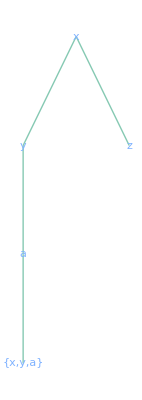

```mathematica
AncestralNestTree[{#}&,Tree[x,{Tree[y,{a}],Tree[z,{}]}]]
```